```mathematica
$Path=Union[{NotebookDirectory[],$Path}];
Get@"SVG`"
```

```mathematica
?SVG`*
```

SVG`ExportSVG

ExportSVG[SVG`Private`gr:Blank[Graphics]]:=SVG`Private`distributeDirectives[First[SVG`Private`gr]]

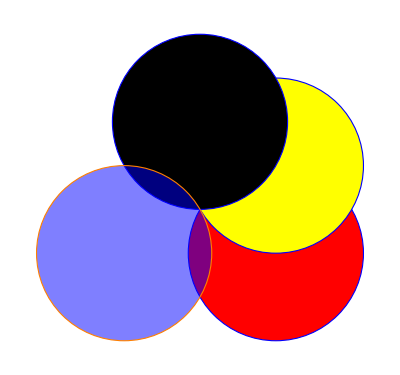

```mathematica
gr=Graphics[{EdgeForm[Directive[Dashed,Blue,Thick]],{Red,Disk[#],{Yellow,Disk[#+{0,1}]}},Disk[#2],{Blue,EdgeForm@Orange,FaceForm@Opacity@.5,Disk[#3]}}&@@CirclePoints[3]]
```

```mathematica
data=ExportString[#,"XML"]&/@Flatten@ExportSVG@gr//Column
```

<circle fill='RGBColor[1, 0, 0]' posSpec='to be done' />
<circle fill='RGBColor[1, 1, 0]' posSpec='to be done' />
<circle fill='GrayLevel[0]' posSpec='to be done' />
<circle fill='RGBColor[0, 0, 1]' posSpec='to be done' />